# Amplitude Modulation Analysis

It is possible to look at the theory of the generation of an amplitude modulated signal in four steps: 
I) Carrier signal
II) Modulating signal
III) Overall modulated signal for a single tone
IV) Expansion to cover a typical audio signal
The idea of ​​amplitude modulation is to transmit a low-frequency signal - voice or music - by modulating a high-frequency (carrier) signal, which is many times larger than the audible range and occupies a narrow frequency band in the radio air.  It can be represented in the form of 
                                                                                                                                                                  y(t) = [A + m(t)].C(t) 

where A is our amplitude of the wave, C(t) is the carrier signal modulation 
                                                                                                                                                         C(t) = C sin(ωc + φ) or C.Cos(ωc + φ) is the carrier wave
                                                                                                                                                         
    carrier frequency in Hertz is equal to ωc / 2 π
    C is the carrier amplitude
    φ is the phase of the signal at the start of the reference time, Both C and φ can be omitted to simplify the equation by changing C to “1” and φ to “0”.
and m(t) is the modulating waveform can either be a single tone. This can be represented by a cosine waveform, or the modulating waveform could be a wide variety of frequencies - these can be represented by a series of cosine waveforms added together in a linear fashion.
                                                                                                                                                                    m(t) = M sin(ωm + φ)
                                                                                                                                                                    
Where:
    modulating signal frequency in Hertz is equal to ωm / 2 π
    M is the carrier amplitude
 φ is the phase of the signal at the start of the reference time, Both C and φ can be omitted to simplify the equation by changing C to “1” and φ to “0”.
In general form, a modulation process of a sinusoidal carrier wave may be described by the following equation :  m(t)= A(t). Cos(ωt +ϕ(t))
Substituting in the individual relationships for the carrier and modulating signal, the overall signal becomes:
                                                                                                                                                                y(t) = [A + Mcos(ωmt+φ].sin(ωct)
                                                                                                                                                                
here we are taking example of wave haiving A as 1 and modulating wave form be Cos[x]  having frequency as 1 and carrier wave as function of cos having frequency as 5.
i.e Cos(5x)*[Cos(x)+1]

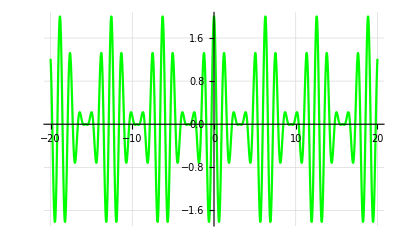

```mathematica
Plot[Cos[5x]*(Cos[x]+1),{x,-20,20},GridLines->Automatic,PlotStyle->{Green},PlotRange->Full]
```

here is our equation carrier wave in mathematical form having frequency of 5 as a carrier:

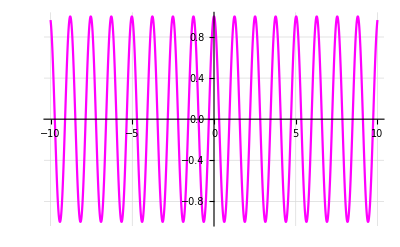

```mathematica
Plot[Cos[5x],{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta}]
```

And the base wave signal itself has a frequency of 1, i.e X_bb:

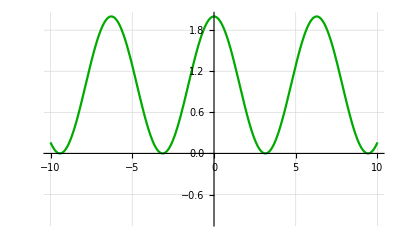

```mathematica
Plot[Cos[x]+1,{x,-10,10},PlotRange->{-1,2},GridLines->Automatic,PlotStyle->{Green//Darker}]
```

You can notice that the signal is shifted upwards and has only positive meanings. This is not accidental and is a mandatory condition for the possibility of its subsequent correct recovery. How to restore 
we have a sinusodial sound wave having equation = m(t)= A(t). Cos(ωt +ϕ(t))

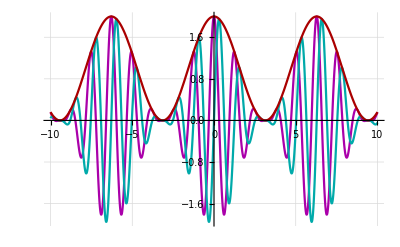

```mathematica
Plot[{
Cos[5x]*(Cos[x]+1),
Sin[5x]*(Cos[x]+1),
√((Cos[5x]*(Cos[x]+1))^2+(Sin[5x]*(Cos[x]+1))^2)
},{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta//Darker,Cyan//Darker,Red//Darker}]
```

the green part represent the carrier wave equation and the magenta and cyan colour are real nd imaginary part of equation, respectively. Here now we analyze our waves w.r.t fourier transformation led to two part of signal the real one and the imaginary one.

SPECTRA FORMATION

Now let’s see what’s happening with the spectra. Let’s calculate the Fourier transform of the carrier signal:  the Fourier transform (FT) is an integral transform that converts a function into a form that describes the frequencies present in the original function. The output of the transform is a complex-valued function of frequency. The term Fourier transform refers to both this complex-valued function and the mathematical operation 
lets begin with the fourier transformation of carrier signal:

```mathematica
FourierTransform[Cos[5x],x,w]
```

√(π/2) DiracDelta[-5+w]+√(π/2) DiracDelta[5+w]

Since the Dirac delta function is not a function in the classical sense, it cannot be graphed in a standard way; so we’ll do it manually, using the generally accepted style:

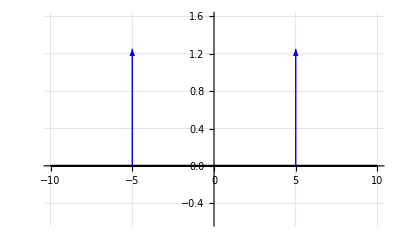

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Black},
Epilog->{Blue,Arrow[{{{-5,0},{-5,√(π/2)}},{{5,0},{5,√(π/2)}}}]}]
```

As expected, we got the same frequency as in the initial formula. The presence of another identical frequency is not accidental - this phenomenon is called Hermitian symmetry and is a consequence of the fact that the function in question is purely real and in the complex representation has a zero imaginary component. The absence of imaginary components in the spectrum after the transformation is due to the fact that initially our functions are also even (symmetric about zero).

Now let’s do the Fourier transform for the based signal :

```mathematica
FourierTransform[Cos[x]+1,x,w]
```

√(π/2) DiracDelta[-1+w]+√(2 π) DiracDelta[w]+√(π/2) DiracDelta[1+w]

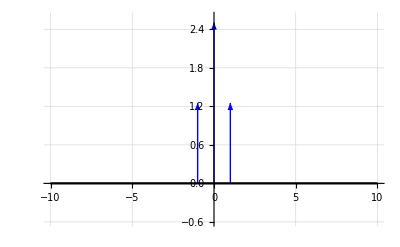

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,2.6},GridLines->Automatic,PlotStyle->{Black},
Epilog->{Blue,Arrow[{{{-1,0},{-1,√(π/2)}},{{0,0},{0,√(2π)}},{{1,0},{1,√(π/2)}}}]}]
```

in the above digram we see three terms can be seen which represent the carrier, and upper and lower sidebands:

Carrier:     A . Cos (ωc +1)
Upper sideband:     A . M/2 [ sin ((ωc + ωm) t + φ)
Lower sideband:     A . M/2 [ sin ((ωc - ωm) t - φ)

where the  sidebands are separated from the carrier by a frequency equal to that of the tone. It can be seen that for a case where there is 100% modulation, i.e. M = 1, and where the carrier is not suppressed, i.e. A = 1, then the sidebands have half the value of the carrier, i.e. a quarter of the power each.


Here we additionally obtained the Dirac delta function at the coordinate center — due to the presence of a constant component in the signal, which does not oscillate by definition —, which allows us to consider it as a zero frequency.

Now we analyze for the whole of wave equation that we are using intialy-->

```mathematica
FourierTransform[Cos[5x](Cos[x]+1),x,w]
```

1/2 √(π/2) DiracDelta[-6+w]+√(π/2) DiracDelta[-5+w]+1/2 √(π/2) DiracDelta[-4+w]+1/2 √(π/2) DiracDelta[4+w]+√(π/2) DiracDelta[5+w]+1/2 √(π/2) DiracDelta[6+w]

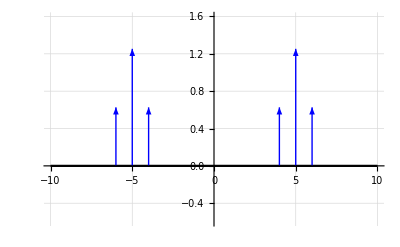

```mathematica
Plot[0,{x,-10,10},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Black},
Epilog->{Blue,Arrow[{{{-6,0},{-6,√(π/8)}},{{-5,0},{-5,√(π/2)}},{{-4,0},{-4,√(π/8)}},
{{4,0},{4,√(π/8)}},{{5,0},{5,√(π/2)}},{{6,0},{6,√(π/8)}}}]}]
```

And now we do the reverse Fourier transformation, forming the initial equation and graphs using fourier transformation

```mathematica
InverseFourierTransform[1/2 √(π/2) DiracDelta[4+w]+√(π/2) DiracDelta[5+w]+1/2 √(π/2) DiracDelta[6+w],w,x]
```

1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2

Since the function is complex, to construct its graph it is necessary to separately extract the actual and imaginary components:

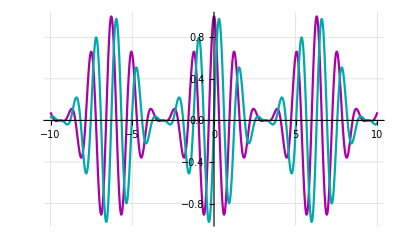

```mathematica
Plot[{
1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2//Re,
1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2//Im
},{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta//Darker,Cyan//Darker,Green//Darker}]
```

Now, in our signal, an imaginary component has appeared, which represents the initial signal shifted by 90 degrees. This will be more obvious if you present the obtained function in trigonometric form:

```mathematica
1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2//ExpToTrig
```

1/4 (1+Cos[x]+ⅈ Sin[x])^2 (Cos[4 x]+ⅈ Sin[4 x])

simplify more to get back the orginal equation we are stated with

```mathematica
1/4 (1+Cos[x]+ⅈ Sin[x])^2 (Cos[4 x]+ⅈ Sin[4 x])//Simplify
```

Cos[x/2]^2 (Cos[5 x]+ⅈ Sin[5 x])

Now it’s more similar to the truth - and as we can see, the function of our output signal has also been simplified. We will try to return it to the original version:

```mathematica
Cos[x/2]^2//TrigReduce
```

1/2 (1+Cos[x])

Forming the carrier equation graph as above using fourier equation transformation

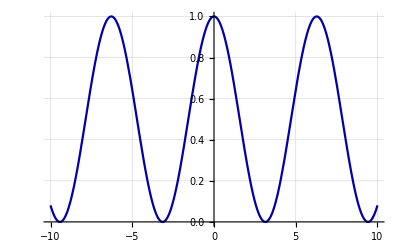

```mathematica
Plot[{
Cos[x/2]^2 (Cos[5 x]-ⅈ Sin[5 x])//Abs
},{x,-10,10},GridLines->Automatic,PlotStyle->{Blue//Darker}]
```

The module of a complex number is calculated every time through the root of the sum of the squares of imaginary and real components. And from here it is clear why the coded signal should consist only of positive values ​​- if it includes negative values, then after restoration they will also become positive.

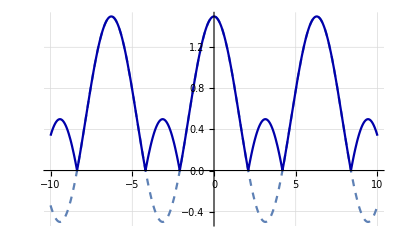

```mathematica
Plot[{
(1/2+Cos[x]),
(1/2+Cos[x])(Cos[5 x]-ⅈ Sin[5 x])//Abs
},{x,-10,10},GridLines->Automatic,PlotStyle->{Dashed,Blue//Darker}]
```

```mathematica
FourierTransform[(Cos[5 x]+I Sin[5 x]),x,w]
```

√(2 π) DiracDelta[5+w]

```mathematica
√(2 π) DiracDelta[5+w]
```

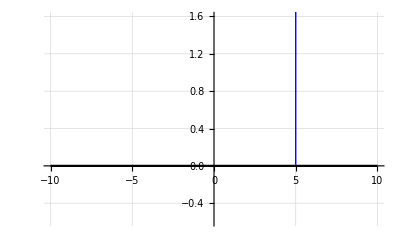

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Black},
Epilog->{Blue,Arrow[{{{5,0},{5,√(2π)}}}]}]
```

```mathematica
FourierTransform[(1+Cos[x])Cos[5 x]*(Cos[5 x]+I Sin[5 x]),x,w]
```

1/2 √(π/2) DiracDelta[-1+w]+√(π/2) DiracDelta[w]+1/2 √(π/2) DiracDelta[1+w]+1/2 √(π/2) DiracDelta[9+w]+√(π/2) DiracDelta[10+w]+1/2 √(π/2) DiracDelta[11+w]